Nacho’s solution and parameters

g_k = 0.03015

κ = 0.439527

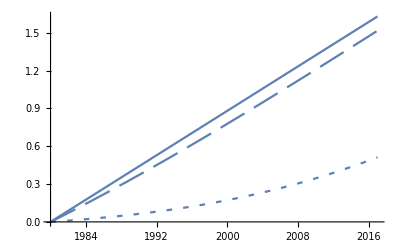

0.113099

```mathematica
θ=1/3;ρ=0.04;δ=0.08;
η=0.21370396;χ=0.22;γ=0.83;
nn=0.0139;

γg=0.0223;γs=0.0065;γx=0.0201;
Ag0=1;As0=1;Ax0=1;

gpg=γx-γg;
gps=γx-γs;
gk=γx/(1-θ);
Print["g_k = ",gk]

κ=(ρ+δ+χ gps+(1-χ)gk)/θ;
Print["κ = ",κ]

k0=κ^(1/(θ-1)) Ax0^(1/(1-θ));
e0=(κ-δ-nn-gk)k0;
y0=κ k0;

Pg[t_]=ⅇ^(gpg(t-1980));
Ps[t_]=ⅇ^(gps(t-1980));
e[t_]=e0 ⅇ^(gk(t-1980));
k[t_]=k0 ⅇ^(gk(t-1980));
y[t_]=y0 ⅇ^(gk(t-1980));
m[t_]=y[t]-δ k[t];

ν[t_]=e[t]^(χ-1)/Ps[t];

V[exp_,pg_,ps_]=1/χ(exp/ps)^χ-η/γ(pg/ps)^γ-1/χ+η/γ;

indu[m_,pg_,ps_,nu_]=V[(nu ps^χ)^(1/(χ-1)),pg,ps]+nu(m-(nu ps^χ)^(1/(χ-1)));
expf[w_,pg_,ps_,nu_]=(nu ps^χ)^(1/(χ-1))+w/nu-V[(nu ps^χ)^(1/(χ-1)),pg,ps]/nu;
Mhat[t_,z_]=expf[indu[m[z],Pg[z],Ps[z],ν[t]],Pg[t],Ps[t],ν[t]];

fig2017=Plot[Log[Mhat[2017,z]]-Log[Mhat[2017,1980]]+nn(z-1980),{z,1980,2017},PlotStyle->Dashing[{0.01,0.02}]];
fig1980=Plot[Log[Mhat[1980,z]]-Log[Mhat[1980,1980]]+nn(z-1980),{z,1980,2017},PlotStyle->Dashing[{0.05,0.02}]];
figM=Plot[Log[m[z]]-Log[m[1980]]+nn(z-1980),{z,1980,2017}];
fig=Show[fig2017,fig1980,figM,PlotRange->All]

Log[m[2017]]-Log[Mhat[1980,2017]]
```

NDP

0.877478

0.015595

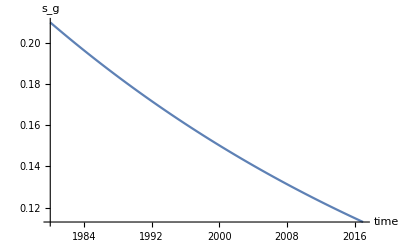

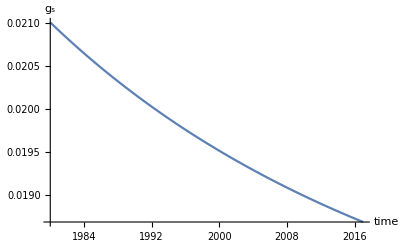

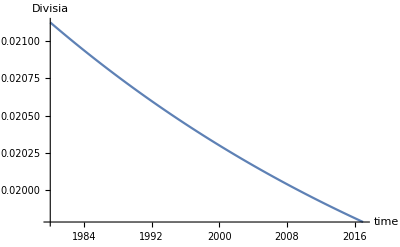

```mathematica
se=e[1980]/m[1980]

gg=(1-χ)gk+(γ-1)gpg+(χ-γ)gps

sg[t_]=η(e[t]/Ps[t])^-χ(Pg[t]/Ps[t])^γ;
Plot[sg[t],{t,1980,2017},AxesLabel->{"time","s_g"}]

Cs[t_]=e[t]/Ps[t](1-sg[t]);
Plot[Cs[t],{t,1980,2017}];
gs[t_]=Simplify[D[Log[Cs[t]],t]];
Plot[gs[t],{t,1980,2017},AxesLabel->{"time","g_s"}]

Divisia[t_]=Simplify[se(sg[t]gg+(1-sg[t])gs[t])+(1-se)gk];
Plot[Divisia[t],{t,1980,2017},AxesLabel->{"time","Divisia"}]
```

```mathematica
FS=Table[{n,NIntegrate[Divisia[t],{t,1980,n}]+nn(n-1980)},{n,1980,2017,0.01}];
```

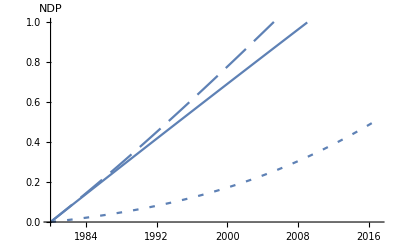

```mathematica
ListPlot[FS,Joined -> True,AxesLabel->{"","NDP"},PlotRange->{{1980,2017},{0,1}}];
Show[%,fig2017,fig1980,PlotRange->{{1980,2017},{0,1}}]
```

GDP

0.717765

0.015595

-Graphics-

-Graphics-

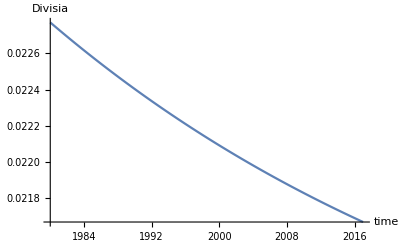

```mathematica
se=e[1980]/y[1980]

gg=(1-χ)gk+(γ-1)gpg+(χ-γ)gps

sg[t_]=η(e[t]/Ps[t])^-χ(Pg[t]/Ps[t])^γ;
Plot[sg[t],{t,1980,2017},AxesLabel->{"time","s_g"}]

Cs[t_]=e[t]/Ps[t](1-sg[t]);
Plot[Cs[t],{t,1980,2017}];
gs[t_]=Simplify[D[Log[Cs[t]],t]];
Plot[gs[t],{t,1980,2017},AxesLabel->{"time","g_s"}]

Divisia[t_]=Simplify[se(sg[t]gg+(1-sg[t])gs[t])+(1-se)gk];
Plot[Divisia[t],{t,1980,2017},AxesLabel->{"time","Divisia"}]
```

```mathematica
FS=Table[{n,NIntegrate[Divisia[t],{t,1980,n}]+nn(n-1980)},{n,1980,2017,0.01}];
```

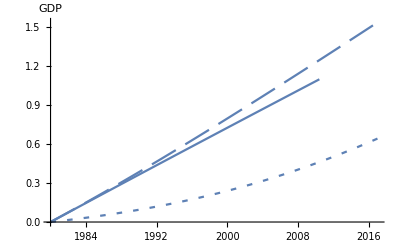

```mathematica
Mhat[t_,z_]=expf[indu[y[z],Pg[z],Ps[z],ν[t]],Pg[t],Ps[t],ν[t]];

fig2017=Plot[Log[Mhat[2017,z]]-Log[Mhat[2017,1980]]+nn(z-1980),{z,1980,2017},PlotStyle->Dashing[{0.01,0.02}]];
fig1980=Plot[Log[Mhat[1980,z]]-Log[Mhat[1980,1980]]+nn(z-1980),{z,1980,2017},PlotStyle->Dashing[{0.05,0.02}]];

ListPlot[FS,Joined -> True,AxesLabel->{"","GDP"},PlotRange->{{1980,2017},{0,1.1}}];
Show[%,fig2017,fig1980,PlotRange->All]
```

```mathematica
γγ
```